## New streamlined notebook for Rb-87

```mathematica
invcminHartree = 4.5563352812122295*10^-6;
BohrinAngstrom=0.529177210903;
AngstrominBohr = 1/0.529177210903;
HartreePerMHz=6.579683920502*10^9;
MHzPerHartree = 1/HartreePerMHz;
nkinHartree=3.1668115634556 10^-15;
amu=(1.66053906660 10^-27)/(9.1093837015 10^-31);
mLi7=amu 7.01600455000;
μLi7=mLi7/2;
massRb87 = 86.909180527*amu;
massRb85 =84.911789738*amu;
μRb87 = massRb87/2;
μRb85 = massRb85/2;
Off[ClebschGordan::phy]
Off[General::munfl]
```

```mathematica
C6 = 0.2270032*10^8;
C8 = 0.7782886 *10^9;
C10 = 0.2868869*10^11;
Cvals={C6 invcminHartree AngstrominBohr^6,C8 invcminHartree AngstrominBohr^8,C10 invcminHartree AngstrominBohr^10}
```

{4710.22,576696.,7.59128×10^7}

```mathematica
βRb87=Select[β/.NSolve[(-C6*AngstrominBohr^6*invcminHartree)/β^6-(C8*AngstrominBohr^8*invcminHartree)/β^8-(C10*AngstrominBohr^10*invcminHartree)/β^10==-1/(2 μRb87 β^2),β],Positive][[1]]
```

165.464

```mathematica
BohrinRb87vdw = 1/βRb87
Rb87vdwinHartree = 1/(2 μRb87 βRb87^2);
HartreeinRb87vdw = 1/Rb87vdwinHartree
```

0.00604361

4.33743×10^9

```mathematica
C6vdw = (2 μRb87)/βRb87^4(C6*invcminHartree*AngstrominBohr^6)
C8vdw = (2 μRb87)/βRb87^6(C8*invcminHartree*AngstrominBohr^8)
C10vdw = (2 μRb87)/βRb87^8(C10*invcminHartree*AngstrominBohr^10)
```

0.995527

0.00445197

0.0000214049

```mathematica
Rb87vlr[r_]:= -C6vdw/r^6-C8vdw/r^8-C10vdw/r^10(*-C26vdw/r^26*);
```

```mathematica
VLongRange[μ_,l_,Cvals_,r_]:=-Cvals[[1]]/r^6-Cvals[[2]]/r^8-Cvals[[3]]/r^10+(l(l+1))/(2μ r^2)
```

```mathematica
Lmax=4;
χplus[L_,R_]:=√R BesselJ[-1/4(2L+1),1/(2 R^2)];
χminus[L_,R_]:=√R BesselJ[1/4(2L+1),1/(2 R^2)];
χmprime[L_,r_]:=(-L r^2 BesselJ[1/4 (1+2 L),1/(2 r^2)]+BesselJ[1/4 (5+2 L),1/(2 r^2)])/r^(5/2);
χpprime[L_,r_]:=((1+L) r^2 BesselJ[1/4 (-1-2 L),1/(2 r^2)]+BesselJ[1/4 (3-2 L),1/(2 r^2)])/r^(5/2);
ksqr[ϵ_,l_,r_]:=ϵ-VLongRange[1/2,l,Cvalsvdw,r];
BC1[ϵ_,l_,r_]=Simplify[Evaluate[(ksqr[ϵ,l,r])^(-1/4)]];
BC2[ϵ_,l_,r_]=Simplify[Evaluate[D[(ksqr[ϵ,l,r])^(-1/4),r]]];
```

```mathematica
ϵtest=0.0;
rx=0.05;
rf=2.0;
nr=300;
αsol=Flatten[Table[NDSolve[{α''[r]+ksqr[ϵtest,l,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵtest,l,rx],α'[rx]==BC2[ϵtest,l,rx]},α,{r,rx,rf}],{l,0,Lmax}]];
αfun=Table[α/.αsol[[i]],{i,1,Length[αsol]}];
rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable=Table[Flatten[{0,Table[NIntegrate[(αfun[[ltest+1]][rp])^-2/.αsol,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,Lmax}];
phaseintfun=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,Lmax}];
```

Now using (ⅆf^0(r))/ⅆr=(α'(r))/(α(r))f^0(r)-1/(α^2(r)) g^0(r)
(ⅆg^0(r))/ⅆr=(α'(r))/(α(r))g^0(r)+1/(α^2(r)) f^0(r)

```mathematica
basepairs[l_,ϕ_,α_,phaseint_,r_]:=Module[{αp,rp,f0,g0,f0p,g0p,χm,χmp},
αp=D[α[rp],rp]/.rp->r;
g0=(-α[r])/(√π)Cos[ϕ+phaseint[r]];
f0=α[r]/(√π)Sin[ϕ+phaseint[r]];
f0p=αp/α[r] f0-1/α[r]^2 g0;
g0p=αp/α[r] g0+1/α[r]^2 f0;
χm=χminus[l,r];
χmp=χmprime[l,r];
{f0,g0,f0p,g0p,χm,χmp}]
```

```mathematica
tanphi=Table[{f0,g0,f0p,g0p,χm,χmp}=basepairs[ltest,0.0,αfun[[ltest+1]],phaseintfun[[ltest+1]],rf];-(χm g0p-χmp g0)/(χm f0p-χmp f0),{ltest,0,Lmax}]
Table[Tan[-1/(2 rx^2)+(L π)/4-(5π)/8],{L,0,Lmax}]
ϕvals=ArcTan[tanphi]
g0function[ϕ_,α_,phaseintfun_,r_]:=(-α[r])/(√π)Cos[ϕ+phaseintfun[r]]
f0function[ϕ_,α_,phaseintfun_,r_]:=α[r]/(√π)Sin[ϕ+phaseintfun[r]]
```

{-1.263,-0.117485,0.785684,8.07589,-1.29596}

{-1.26422,-0.116693,0.791003,8.56951,-1.26422}

{-0.901098,-0.116949,0.665951,1.4476,-0.913598}

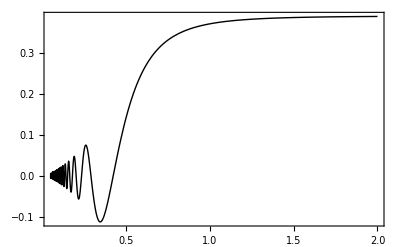

```mathematica
ltest=0;Plot[g0function[ϕvals[[ltest+1]],αfun[[ltest+1]],phaseintfun[[ltest+1]],r],{r,rx,rf},PlotRange->All,PlotStyle->{Black,Thin},Frame->True]
```

## Hyperfine and Zeeman interactions for Rb

```mathematica
Rb87AMHz = 3417.3413064215;
Rb85AMHz = 1011.9108132;
Rb87gi = -0.000995141410;
Rb85gi = -0.00029364006;
Rb87gs = 2.002319313470;
Rb85gs = Rb87gs;
Rb87s = 1/2;
Rb85s = Rb87s;
Rb87i = 3/2;
Rb85i = 5/2;
(*1-atom HF basis*)
Rb87HFbasis = Flatten[Table[Table[{f, mf},{mf,-f,f}],{f,1,2}],1]
Rb85HFbasis=Flatten[Table[Table[{f, mf},{mf,-f,f}],{f,2,3}],1];
(*Nuclear and Bohr Magnetons (MHz/G)*)
μb = (9.27*10^-24)/(6.626*10^-34)*10^-10;
μn = (5.0507837461*10^-27)/(6.626*10^-34)*10^-10;
```

{{1,-1},{1,0},{1,1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}

Converting to Atomic Units

```mathematica
Rb87ATHz = Rb87AMHz*10^-6;
Rb85ATHz = Rb85AMHz*10^-6;
Rb87Ainvcm = (Rb87ATHz *6.626*10^-34*10^12)/(1.986*10^-23);
Rb85Ainvcm = (Rb85ATHz *6.626*10^-34*10^12)/(1.986*10^-23);
Rb87AH = Rb87Ainvcm*invcminHartree;
Rb85AH = Rb85Ainvcm*invcminHartree;
μbTHz = μb *10^-6;
μnTHz = μn*10^-6;
μbinvcm = (μbTHz *6.626*10^-34*10^12)/(1.986*10^-23);
μninvcm = (μnTHz *6.626*10^-34*10^12)/(1.986*10^-23);
μbH=μbinvcm*invcminHartree;
μnH=μninvcm*invcminHartree;
```

```mathematica
Hhf[A_,i_,s_,f_,ℏ_]:= A/2 ℏ^2(f(f+1)-s(s+1)-i(i+1));
Hz[fp_,mp_,f_,m_,gi_,gs_,s_,i_,B_]:= gs μbH B √((2 fp +1)(2f +1)) Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]-gi μbH B √((2 fp +1)(2f +1)) Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

Rubidium-87 (1-atom HF and Zeeman)

```mathematica
HhfRb87Table=Table[Hhf[Rb87AH,Rb87i,Rb87s,Rb87HFbasis[[j,1]],1]KroneckerDelta[j,jp],{j,1,8},{jp,1,8}]
```

{{-6.49361×10^-7,0.,0.,0.,0.,0.,0.,0.},{0.,-6.49361×10^-7,0.,0.,0.,0.,0.,0.},{0.,0.,-6.49361×10^-7,0.,0.,0.,0.,0.},{0.,0.,0.,3.89617×10^-7,0.,0.,0.,0.},{0.,0.,0.,0.,3.89617×10^-7,0.,0.,0.},{0.,0.,0.,0.,0.,3.89617×10^-7,0.,0.},{0.,0.,0.,0.,0.,0.,3.89617×10^-7,0.},{0.,0.,0.,0.,0.,0.,0.,3.89617×10^-7}}

```mathematica
HzRb87Table[B_]:= Table[Hz[Rb87HFbasis[[jp,1]],Rb87HFbasis[[jp,2]],Rb87HFbasis[[j,1]],Rb87HFbasis[[j,2]],Rb87gi,Rb87gs,Rb87s,Rb87i,B],{j,1,8},{jp,1,8}];
```

```mathematica
HRb87[B_]:= HzRb87Table[B] + HhfRb87Table;
```

```mathematica
Rb87AtomEigenSystem[B_]:=Sort[Transpose[Eigensystem[HRb87[B]]]]
Rb87AtomEth[B_]:=Table[Rb87AtomEigenSystem[B][[i]][[1]],{i,1,8}]
Rb87EigenSystem[B_]:=Sort[Eigenvalues[HRb87[B]]];
```

```mathematica
(*Plot[{Rb87EigenSystem[B][[1]],Rb87EigenSystem[B][[2]],Rb87EigenSystem[B][[3]],Rb87EigenSystem[B][[4]],Rb87EigenSystem[B][[5]],Rb87EigenSystem[B][[6]],Rb87EigenSystem[B][[7]],Rb87EigenSystem[B][[8]]},{B,1,2000}, Frame->True,FrameLabel->{"B [G]","Energy [Hartree]"},ImageSize->Large,LabelStyle->Large ]*)
```

```mathematica
hartreetoK = 3.1577502480407*10^5;
```

```mathematica
(*Plot[{Rb87EigenSystem[B][[1]]*hartreetoK,Rb87EigenSystem[B][[2]]*hartreetoK,Rb87EigenSystem[B][[3]]*hartreetoK,Rb87EigenSystem[B][[4]]*hartreetoK,Rb87EigenSystem[B][[5]]*hartreetoK,Rb87EigenSystem[B][[6]]*hartreetoK,Rb87EigenSystem[B][[7]]*hartreetoK,Rb87EigenSystem[B][[8]]*hartreetoK},{B,1,2000}, Frame->True,FrameLabel->{"B [G]","Energy [K]"},ImageSize->Large,LabelStyle->Large ]*)
```

Rubidium-85 (1-atom HF and Zeeman)

```mathematica
HhfRb85Table=Table[Hhf[Rb85AH,Rb85i,Rb85s,Rb85HFbasis[[j,1]],1]KroneckerDelta[j,jp],{j,1,Length[Rb85HFbasis]},{jp,1,Length[Rb85HFbasis]}];
HzRb85Table[B_]:= Table[Hz[Rb85HFbasis[[jp,1]],Rb85HFbasis[[jp,2]],Rb85HFbasis[[j,1]],Rb85HFbasis[[j,2]],Rb85gi,Rb85gs,Rb85s,Rb85i,B],{j,1,Length[Rb85HFbasis]},{jp,1,Length[Rb85HFbasis]}];
HRb85[B_]:= HzRb85Table[B] + HhfRb85Table;
Rb85AtomEigenSystem[B_]:=Sort[Transpose[Eigensystem[HRb85[B]]]]
Rb85AtomEth[B_]:=Table[Rb85AtomEigenSystem[B][[i]][[1]],{i,1,Length[Rb85HFbasis]}]
Rb85EigenSystem[B_]:=Sort[Eigenvalues[HRb85[B]]];
```

```mathematica
(*Plot[{Rb85EigenSystem[B][[1]]*hartreetoK,Rb85EigenSystem[B][[2]]*hartreetoK,Rb85EigenSystem[B][[3]]*hartreetoK,Rb85EigenSystem[B][[4]]*hartreetoK,Rb85EigenSystem[B][[5]]*hartreetoK,Rb85EigenSystem[B][[6]]*hartreetoK,Rb85EigenSystem[B][[7]]*hartreetoK,Rb85EigenSystem[B][[8]]*hartreetoK,Rb85EigenSystem[B][[9]]*hartreetoK,Rb85EigenSystem[B][[10]]*hartreetoK,Rb85EigenSystem[B][[11]]*hartreetoK,Rb85EigenSystem[B][[12]]*hartreetoK},{B,1,1000}, Frame->True,FrameLabel->{"B [G]","Energy [K]"},ImageSize->Large,LabelStyle->Large ]*)
```

```mathematica
Rb87HF2atombasis =Sort[ Flatten[Table[Table[{f1, mf1,f2,mf2},{mf1,-f1,f1},{mf2,-f2,f2}],{f1,1,2},{f2,1,2}],3]];
```

```mathematica
mF2unsym =Select[Rb87HF2atombasis,#[[2]]+#[[4]]==2&]
```

{{1,0,2,2},{1,1,1,1},{1,1,2,1},{2,0,2,2},{2,1,1,1},{2,1,2,1},{2,2,1,0},{2,2,2,0}}

Keep only those 1-atom states that produce a unique symmetrized state

```mathematica
mF2basis = {{1,0,2,2},{1,1,1,1},{1,1,2,1},{2,0,2,2},{2,1,2,1}};
```

```mathematica
ProjectionCoefficient[f1_,m1_,f2_,m2_,s_,ms_,i_,mi_,s1_,i1_,s2_,i2_]:= (-1)^(2i2-2s1-m1-m2-ms-mi)√((2f1+1)(2f2+1)(2s+1)(2i+1)) Sum[ThreeJSymbol[{s1,ms1},{i1,mi1},{f1, -m1}]*ThreeJSymbol[{s2,ms2},{i2,mi2},{f2,-m2}]*ThreeJSymbol[{s1,ms1},{s2,ms2},{s,-ms}]*ThreeJSymbol[{i1,mi1},{i2,mi2},{i,-mi}],{ms1,-s1,s1},{mi1,-i1,i1},{ms2,-s2,s2},{mi2,-i2,i2}];

ProjectionMatrixElement[f1_,m1_,f1p_,m1p_,f2_,m2_,f2p_,m2p_,s1_,i1_,s2_,i2_,S_]:= Sum[Sum[ProjectionCoefficient[f1,m1,f2,m2,s,ms,i,mi,s1,i1,s2,i2]*ProjectionCoefficient[f1p,m1p,f2p,m2p,s,ms,i,mi,s1,i1,s2,i2]*KroneckerDelta[s,S],{ms,-s,s},{mi,-i,i}],{s,Abs[s1-s2],Abs[s1+s2]},{i,Abs[i1-i2],Abs[i1+i2]}];
SingletProjectionMatrix= Table[Sum[Sum[ProjectionCoefficient[mF2unsym[[j,1]],mF2unsym[[j,2]],mF2unsym[[j,3]],mF2unsym[[j,4]],s,ms,i,mi,Rb87s,Rb87i,Rb87s,Rb87i]*ProjectionCoefficient[mF2unsym[[jp,1]],mF2unsym[[jp,2]],mF2unsym[[jp,3]],mF2unsym[[jp,4]],s,ms,i,mi,Rb87s,Rb87i,Rb87s,Rb87i] *KroneckerDelta[s,0],{ms,-s,s},{mi,-i,i}],{s,0,1},{i,0,3}],{j,1,8},{jp,1,8}];
```

```mathematica
SingletProjectionSym[p_,l_]:= Table[(1/(2√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Rb87s,Rb87i,Rb87s,Rb87i,0]+ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Rb87s,Rb87i,Rb87s,Rb87i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Rb87s,Rb87i,Rb87s,Rb87i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Rb87s,Rb87i,Rb87s,Rb87i,0]),{j,1,5},{jp,1,5}]
```

```mathematica
(*SProjSymRb87=FullSimplify[SingletProjectionSym[0,0]]*)
(*TripletProjectionMatrix = Table[Sum[Sum[ProjectionCoefficient[mF2unsym[[j,1]],mF2unsym[[j,2]],mF2unsym[[j,3]],mF2unsym[[j,4]],s,ms,i,mi,Rb87s,Rb87i,Rb87s,Rb87i]*ProjectionCoefficient[mF2unsym[[jp,1]],mF2unsym[[jp,2]],mF2unsym[[jp,3]],mF2unsym[[jp,4]],s,ms,i,mi,Rb87s,Rb87i,Rb87s,Rb87i]* KroneckerDelta[s,1],{ms,-s,s},{mi,-i,i}],{s,0,1},{i,0,3}],{j,1,8},{jp,1,8}];*)

(*TripletProjectSym[p_,l_]:=Table[(1/(2√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Rb87s,Rb87i,Rb87s,Rb87i,1]+ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Rb87s,Rb87i,Rb87s,Rb87i,1]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Rb87s,Rb87i,Rb87s,Rb87i,1]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Rb87s,Rb87i,Rb87s,Rb87i,1]),{j,1,5},{jp,1,5}] *)
```

```mathematica
Rb87SingletProjection={{3/16,(√(3/2))/8,-(√3)/8,(√3)/8,-3/16},{(√(3/2))/8,1/8,-1/(4 √2),1/(4 √2),-(√(3/2))/8},{-(√3)/8,-1/(4 √2),1/4,-1/4,(√3)/8},{(√3)/8,1/(4 √2),-1/4,1/4,-(√3)/8},{-3/16,-(√(3/2))/8,(√3)/8,-(√3)/8,3/16}};
Rb87TripletProjection={{13/16,-(√(3/2))/8,(√3)/8,-(√3)/8,3/16},{-(√(3/2))/8,7/8,1/(4 √2),-1/(4 √2),(√(3/2))/8},{(√3)/8,1/(4 √2),3/4,1/4,-(√3)/8},{-(√3)/8,-1/(4 √2),1/4,3/4,(√3)/8},{3/16,(√(3/2))/8,-(√3)/8,(√3)/8,13/16}};
```

```mathematica
N[MatrixForm[Rb87SingletProjection]]
```

(0.1875 | 0.153093 | -0.216506 | 0.216506 | -0.1875
0.153093 | 0.125 | -0.176777 | 0.176777 | -0.153093
-0.216506 | -0.176777 | 0.25 | -0.25 | 0.216506
0.216506 | 0.176777 | -0.25 | 0.25 | -0.216506
-0.1875 | -0.153093 | 0.216506 | -0.216506 | 0.1875)

```mathematica
N[MatrixForm[Rb87TripletProjection]]
```

(0.8125 | -0.153093 | 0.216506 | -0.216506 | 0.1875
-0.153093 | 0.875 | 0.176777 | -0.176777 | 0.153093
0.216506 | 0.176777 | 0.75 | 0.25 | -0.216506
-0.216506 | -0.176777 | 0.25 | 0.75 | 0.216506
0.1875 | 0.153093 | -0.216506 | 0.216506 | 0.8125)

```mathematica
HZ[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_,μb_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μb B Sqrt[(2fp+1)(2f+1)]Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]-gi μb B Sqrt[(2fp+1)(2f+1)]Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

```mathematica
HZsym[p_,l_,B_]:=Table[(1/(√((1+KroneckerDelta[Rb87MF2basis[[j,1]],Rb87MF2basis[[j,3]]] KroneckerDelta[Rb87MF2basis[[j,2]],Rb87MF2basis[[j,4]]])(1+KroneckerDelta[Rb87MF2basis[[jp,1]],Rb87MF2basis[[jp,3]]] KroneckerDelta[Rb87MF2basis[[jp,2]],Rb87MF2basis[[jp,4]]]))))*(HZ[Rb87MF2basis[[j,1]],Rb87MF2basis[[j,2]],Rb87MF2basis[[jp,1]],Rb87MF2basis[[jp,2]],Rb87s,Rb87i,Rb87gs,Rb87gi,Rb87AH,B,μbH]KroneckerDelta[Rb87MF2basis[[j,3]],Rb87MF2basis[[jp,3]]]KroneckerDelta[Rb87MF2basis[[j,4]],Rb87MF2basis[[jp,4]]]+HZ[Rb87MF2basis[[j,3]],Rb87MF2basis[[j,4]],Rb87MF2basis[[jp,3]],Rb87MF2basis[[jp,4]],Rb87s,Rb87i,Rb87gs,Rb87gi,Rb87AH,B,μbH]KroneckerDelta[Rb87MF2basis[[j,1]],Rb87MF2basis[[jp,1]]]KroneckerDelta[Rb87MF2basis[[j,2]],Rb87MF2basis[[jp,2]]]+(-1)^p(-1)^l HZ[Rb87MF2basis[[j,3]],Rb87MF2basis[[j,4]],Rb87MF2basis[[jp,1]],Rb87MF2basis[[jp,2]],Rb87s,Rb87i,Rb87gs,Rb87gi,Rb87AH,B,μbH]KroneckerDelta[Rb87MF2basis[[j,1]],Rb87MF2basis[[jp,3]]]KroneckerDelta[Rb87MF2basis[[j,2]],Rb87MF2basis[[jp,4]]]+(-1)^p(-1)^l HZ[Rb87MF2basis[[j,1]],Rb87MF2basis[[j,2]],Rb87MF2basis[[jp,3]],Rb87MF2basis[[jp,4]],Rb87s,Rb87i,Rb87gs,Rb87gi,Rb87AH,B,μbH]KroneckerDelta[Rb87MF2basis[[j,3]],Rb87MF2basis[[jp,1]]]KroneckerDelta[Rb87MF2basis[[j,4]],Rb87MF2basis[[jp,2]]]),{j,1,Length[Rb87MF2basis]},{jp,1,Length[Rb87MF2basis]}]
```

```mathematica
HZRb87[B_]=FullSimplify[HZsym[0,0,B]];
```

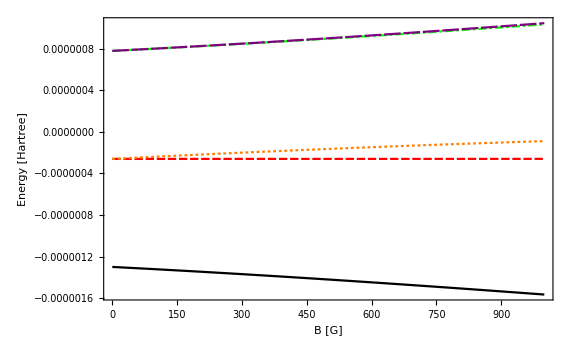

```mathematica
EigenSystemRb87[B_]:= Sort[Transpose[Eigensystem[HZRb87[B]]]];
Plot[{EigenSystemRb87[B][[1]][[1]],EigenSystemRb87[B][[2]][[1]],EigenSystemRb87[B][[3]][[1]],EigenSystemRb87[B][[4]][[1]],EigenSystemRb87[B][[5]][[1]]},{B,0,1000},ImageSize->Large,Frame->True,FrameLabel->{"B [G]","Energy [Hartree]"},LabelStyle->Large,PlotStyle->{Black,Red,Orange,Green,Purple}]
```